# Homework 27

## Problem 27.1

A large artillery shell has a horizontal range of 2.200 km when fired at an angle of alpha=40 degrees above the horizontal. Let z be up and x be the direction of the horizontal component of the initial velocity (due east). 

Let
m = 100 kg be the mass of the shell.
d = 0.35 m be the diameter of the shell.
Omega = 7.27*10^(-5) rad/sec is the angular velocity of the earth.
theta = 50 degrees is the colatitude (90 degrees - latitude).

```mathematica
Quit[]
Clear["`*"]
```

## Part A

Find the muzzle velocity of the shell. The muzzle is located 1.75 m above the ground. Include quadratic drag, assuming that the formula for a sphere applies here. Ignore any effects of the earth’s rotation at this point.

Hint: just keep trying v0 until you get the right range. (Yes, this is just a review...) 
The second graph will help when you get close - Just find v0 to within the nearest 0.1 m/s.

```mathematica
d=0.35;
c=0.25*d^2;
m=100;
g=9.8;
Omega=7.27*10^-5;
theta=50*Pi/180;
alpha=40*Pi/180; (* launch angle *)
z0=1.75;
```

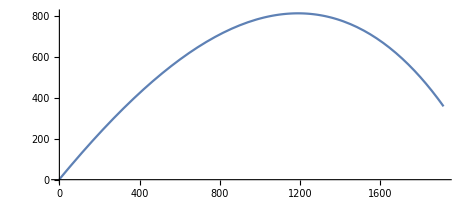

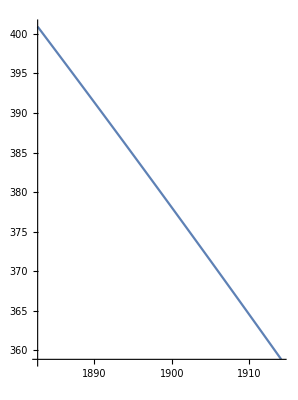

```mathematica
xeq=m*x''[t]==-c*Sqrt[x'[t]^2+z'[t]^2]*x'[t];
zeq=m*z''[t]==-m*g-c*Sqrt[x'[t]^2+z'[t]^2]*z'[t];
v0=200;
sol1=NDSolve[{xeq,zeq,z[0]==z0,x[0]==0,x'[0]==v0*Cos[theta],z'[0]==v0*Cos[alpha]},{x,z},{t,0,22}];
ParametricPlot[{x[t],z[t]}/.sol1,{t,0,22}]
ParametricPlot[{x[t],z[t]}/.sol1,{t,21.5,22}]
```

### Solution to v0

```mathematica
If[FullSimplify[Abs[(v0-198.2)/198.2]<0.01],Print["v0 is correct."],Print["v0 is incorrect."]]
```

v0 is correct.

### Solution to xeq and yeq

```mathematica
xeq$=m*x''[t]==-c*Sqrt[x'[t]^2+z'[t]^2]*x'[t];
x1$=Solve[xeq,x''[t]];
x2$=Solve[xeq$,x''[t]];
If[FullSimplify[x1$]===FullSimplify[x2$],Print["xeq is correct."],Print["xeq is incorrect."]]
zeq$=m*z''[t]==-m*g-c*Sqrt[x'[t]^2+z'[t]^2]*z'[t];
z1$=Solve[zeq,z''[t]];
z2$=Solve[zeq$,z''[t]];
If[FullSimplify[z1$]===FullSimplify[z2$],Print["zeq is correct."],Print["zeq is incorrect."]]
```

xeq is correct.

zeq is correct.

Now we want to measure the range very accurately (to the nearest mm), leaving v0 fixed at the value you found above. We'll need this for comparison later. Adjust the time window and PlotRange as necessary.

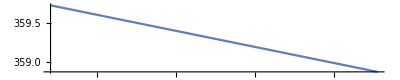

```mathematica
ParametricPlot[{x[t]-2200,z[t]}/.sol1,{t,21.99,22},AspectRatio->1/5,PlotRange->Automatic]
```

There is some variation in the numerical solutions, but I get about 2199.9484 m. Note the trick of subtracting 2200 from the x values, so the axis labels have more significant digits.

## Part B

Now use Equations 9.53 with drag added in to find how much the rotation of the earth affects the location where the the shell strikes the ground. Let the shell be fired due east. (Note that east is the x direction in equation 9.53.)

```mathematica
Xeq=m*x''[t]==-c*Sqrt[x'[t]^2+y'[t]^2+z'[t]^2]*x'[t]+2*m*Omega*(y'[t]*Cos[theta]-z'[t]*Sin[theta]);
Yeq=m*y''[t]==-c*Sqrt[x'[t]^2+y'[t]^2+z'[t]^2]*y'[t]-2*m*Omega*x'[t]*Cos[theta];
Zeq=m*z''[t]==-m*g-c*Sqrt[x'[t]^2+y'[t]^2+z'[t]^2]*z'[t]+2*m*Omega*x'[t]*Sin[theta];
```

### Solutions

```mathematica
Xeq$=m*x''[t]==-c*Sqrt[x'[t]^2+y'[t]^2+z'[t]^2]*x'[t]+2*m*Omega*(y'[t]*Cos[theta]-z'[t]*Sin[theta]);
X1$=Solve[Xeq,x''[t]];
X2$=Solve[Xeq$,x''[t]];
If[FullSimplify[X1$]===FullSimplify[X2$],Print["Xeq is correct."],Print["Xeq is incorrect."]]
Yeq$=m*y''[t]==-c*Sqrt[x'[t]^2+y'[t]^2+z'[t]^2]*y'[t]-2*m*Omega*x'[t]*Cos[theta];
Y1$=Solve[Yeq,y''[t]];
Y2$=Solve[Yeq$,y''[t]];
If[FullSimplify[Y1$]===FullSimplify[Y2$],Print["Yeq is correct."],Print["Yeq is incorrect."]]
Zeq$=m*z''[t]==-m*g-c*Sqrt[x'[t]^2+y'[t]^2+z'[t]^2]*z'[t]+2*m*Omega*x'[t]*Sin[theta];
Z1$=Dz2/.Solve[Zeq,z''[t]];
Z2$=Dz2/.Solve[Zeq$,z''[t]];
If[FullSimplify[Z1$]===FullSimplify[Z2$],Print["Zeq is correct."],Print["Zeq is incorrect."]]
```

Xeq is correct.

Yeq is correct.

Zeq is correct.

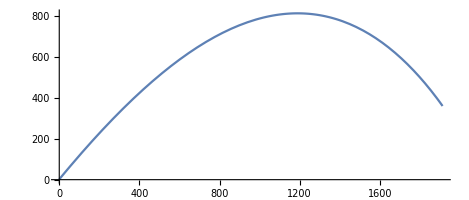

```mathematica
sol2=NDSolve[{Xeq,Yeq,Zeq,z[0]==z0,x[0]==0,x'[0]==v0*Cos[theta],z'[0]==v0*Cos[alpha],y[0]==0, y'[0]==0},{x,y,z},{t,0,22}];
ParametricPlot[{x[t],z[t]}/.sol2,{t,0,22}]
```

And now determine the landing point accurately. As before, adjust the time window and PlotRange as necessary.

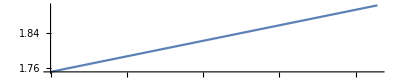

```mathematica
ParametricPlot[{x[t]-2200,z[t]}/.sol2,{t,0,.001},AspectRatio->1/5,PlotRange->Automatic]
```

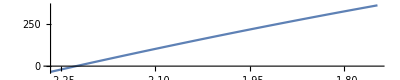

```mathematica
ParametricPlot[{y[t],z[t]}/.sol2,{t,22,26},AspectRatio->1/5,PlotRange->Automatic]
```

Based on your graphs, find Deltax and Deltay, (value with rotational effects minus value without rotational effects)

```mathematica
Deltax=1;
Deltay=-2.2;
```

In terms of the cardinal directions (north, south, east, west), describe how the landing point of the shell has changed as a result of including the rotation of the earth. (Type your answer in this cell.)

### Solutions

```mathematica
If[Abs[(Deltax-1.2100)/1.2100]<0.3,Print["Deltax is about right."],Print["Deltax may be off."]]
If[Abs[(Deltay+1.9671)/1.9671]<0.2,Print["Deltay is about right."],Print["Deltay may be off."]]
```

Deltax is about right.

Deltay is about right.

The landing point has shifted 1.21 meters to the east and 1.9671 meters to the south relative to where it would have landed if the earth were an inertial reference frame.

## Problem 27.2

Work through the Foucault pendulum problem using Mathematica.

Use the following information:
Our latitude is very close to 40 degrees north (so what is theta?). (Actually 40 degrees passes through south Payson.)

L=10.0 m
Omega=7.27*10^-5 rad/sec is the earth's angular velocity.

At t=0, the pendulum is pulled toward the east to x0=1.50 m and then released from rest.

Use the coordinates of the text: z is up, x is east, and y is north.

```mathematica
Quit[]
Clear["`*"]
```

## Part A

Review the first two pages of the text and so that you understand the origin of Eq 9.61.

## Part B

Write down the equations of motion.

```mathematica
xeq=x''[t]==-g*x[t]/L+2*Omega*y'[t]*Cos[theta];
yeq=y''[t]==-g*y[t]/L-2*Omega*x'[t]*Cos[theta];
```

### Solution

```mathematica
xeq$=x''[t]==-g*x[t]/L+2*Omega*y'[t]*Cos[theta];
yeq$=y''[t]==-g*y[t]/L-2*Omega*x'[t]*Cos[theta];
a1$=Solve[xeq$,x''[t]];
a2$=Solve[xeq,x''[t]];
a3$=Solve[yeq$,y''[t]];
a4$=Solve[yeq,y''[t]];
If[FullSimplify[a1$]===FullSimplify[a2$],Print["xeq is correct."],Print["xeq is incorrect."]]
If[FullSimplify[a3$]===FullSimplify[a4$],Print["yeq is correct."],Print["yeq is incorrect."]]
```

xeq is correct.

yeq is correct.

## Part C

Put in numbers.

```mathematica
g=9.8;
L=10.0;
Omega=7.27*10^-5;
theta=50*Pi/180;
x0=1.5;
```

### Solution

```mathematica
theta$=50*Pi/180;
If[FullSimplify[Abs[(theta-theta$)/theta$]<0.02],Print["theta is correct."],Print["theta is incorrect."]]
theta2$=40*Pi/180;
If[FullSimplify[Abs[(theta-theta2$)/theta2$]<0.02],Print["Remember that theta is the colatitude."]]
```

theta is correct.

Solve the equation numerically and plot x(t), y(t).

```mathematica
sol=NDSolve[{xeq,yeq,x[0]==x0,x'[0]==Omega*Cos[theta],y[0]==0,y'[0]==Omega*Sin[theta]},{x,y},{t,0,15}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

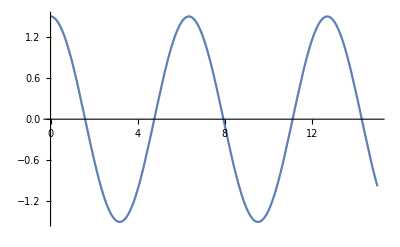

```mathematica
Plot[x[t]/.sol,{t,0,15}]
```

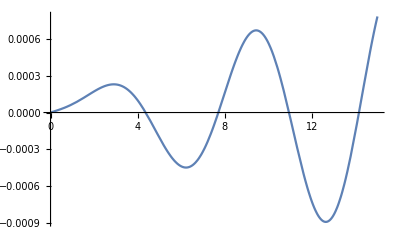

```mathematica
Plot[y[t]/.sol,{t,0,15}]
```

## Part D

Calculate the period of oscillation T.

```mathematica
omega=1/6.3*2*Pi;
T=6.3;
```

### Hint

If you ignore the rotation of the earth, what is the period of oscillation?

### Solution

```mathematica
If[FullSimplify[Abs[(omega-0.989949)/0.989949]<0.01],Print["omega is correct."],Print["omega is incorrect."]]
If[FullSimplify[Abs[(T-6.34698)/6.34698]<0.01],Print["T is correct."],Print["T is incorrect."]]
```

omega is correct.

T is correct.

Plot a cosine function with the frequency found above and compare it with the numerical solution of x(t) to see how well it agrees. Fill in the question marks below with the appropriate cosine function so that the two curves are basically indistinguishable.

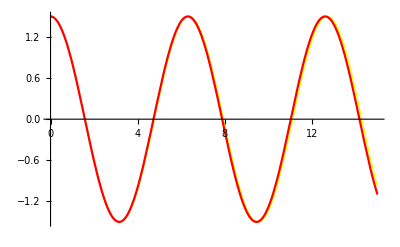

```mathematica
Plot[{x[t]/.sol,x0*Cos[omega*t]},{t,0,15},PlotStyle->{{Yellow,Thick},Red}]
```

### Solution

The correct function is x0*Cos[omega*t]

## Part E

On physical grounds, we expect the x value to be decreasing slightly, while the y value is increasing.(What "physical grounds" require this?)
Also, we expect y (t) to be the product of a simple cosine function (of the same period as x (t)) and a second sine function of a longer period (within the small angle approximation). This longer period is the time it would take the pendulum to swing along the x -axis again. Call this period T2 and its corresponding angular frequency omega2. Either by trial and error or by looking through the section in the textbook, find the value of omega2 that agrees well with the graph of y(t). To refine your guess, zoom in on a portion of the graph. What is the period T2?

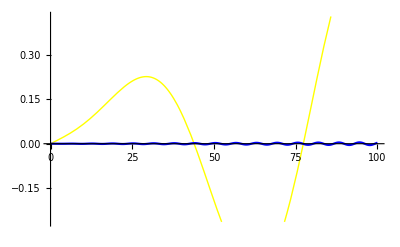

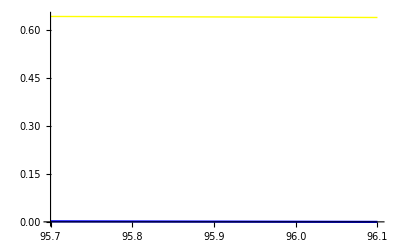

```mathematica
sol2=NDSolve[{xeq,yeq,x[0]==x0,x'[0]==Omega*Cos[theta],y[0]==0,y'[0]==Omega*Sin[theta]},{x,y},{t,0,100}];
omega2=1/134455.3107*2*Pi;
Plot[{y[t]/.sol2,Cos[omega*t]*Sin[omega2*t]},{t,0,100},PlotStyle->{{Yellow,Thick},Blue}]
Plot[{y[t]/.sol2,Cos[omega*t]*Sin[omega2*t]},{t,95.7,96.1},PlotStyle->{{Yellow,Thick},Blue}]
T2=134455.3107;
```

### Solution

```mathematica
T2$=134455.3107;
If[FullSimplify[Abs[(T2-T2$)/T2$]<0.01],Print["T2 is correct. This is about 37 hours and 20 minutes."],Print["T2 is incorrect."]]
```

T2 is correct. This is about 37 hours and 20 minutes.

Now, just for fun, let’s imagine that the earth is spinning 100 times faster about its axis than it really is and that we have a 1000-m pendulum. Execute the code below to visualize the trajectory of the pendulum bob.

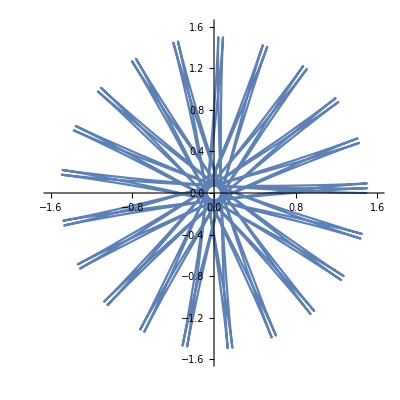

```mathematica
Omega=100*7.27*10^(-5);
L=1000;
tfinal=2*Pi/(Omega*Cos[theta]);
sol3=NDSolve[{xeq,yeq,x[0]==x0,x'[0]==0,y[0]==0,y'[0]==0},{x,y},{t,0,tfinal}];
ParametricPlot[Evaluate[{x[t],y[t]}/.sol3],{t,0,tfinal},PlotRange->{{-1.6,1.6},{-1.6,1.6}}]
Manipulate[ParametricPlot[Evaluate[{x[t],y[t]}/.sol3],{t,0,tf},PlotRange->{{-1.6,1.6},{-1.6,1.6}}],{tf,0.001,tfinal}]
```

## Written Problems

-Graphics-